```mathematica
Solution=NDSolveValue[{D[u[x,y],{x,2}]+D[u[x,y],{y,2}]==0,u[0,y]==0,u[1,y]==0,u[x,0]==0,u[x,1.5]==1},u,{x,0,1},{y,0,1.5}]
```

InterpolatingFunction[…]

```mathematica
Plot3D[Solution[x,y],{x,0,1},{y,0,1.5}]
```

-Graphics3D-

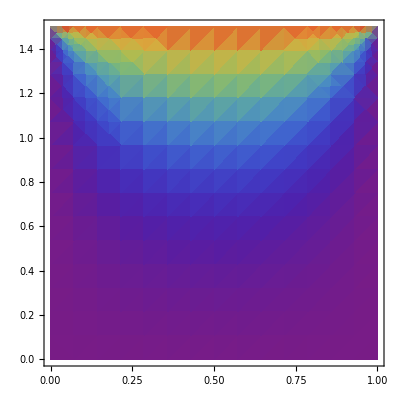

```mathematica
DensityPlot[Solution[x,y],{x,0,1},{y,0,1.5},ColorFunction->"Rainbow"]
```

```mathematica
Solution2=NDSolveValue[{D[u[x,y],{x,2}]+D[u[x,y],{y,2}]==-1,u[0,y]==0,u[1,y]==0,u[x,0]==0,u[x,1]==0},u,{x,0,1},{y,0,1}]
```

InterpolatingFunction[…]

```mathematica
Plot3D[Solution2[x,y],{x,0,1},{y,0,1}]
```

-Graphics3D-

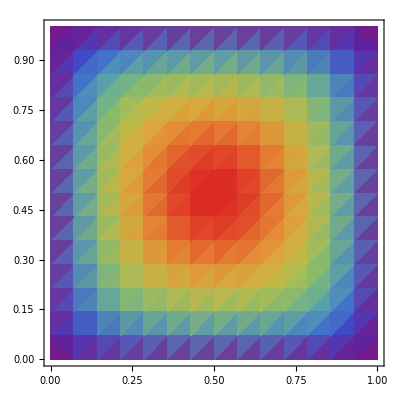

```mathematica
DensityPlot[Solution2[x,y],{x,0,1},{y,0,1},ColorFunction->"Rainbow"]
```